# C&Q Chaos V - Strong chaos phenomenology

We have established what integrable systems are, and where and why their properties are broken. We also discussed that this is connected to infinite folding in the homoclinic tangle near unstable equilibria. 

However, all of this refers to properties of infinitesimal perturbations of integrable systems. Also, we have mentioned the word “chaos” a couple of times without properly defining it. What do we know about non-integrable Hamiltonian systems at finite values of perturbations? And how is chaos defined? This what we will answer in this lecture.

## Defining chaos

Let us start with the definition of a Lyapunov exponent.

### Lyapunov spectrum

Consider a trajectory in a dynamical system z^i(t), where i=1,...D and D is the dimension of the phase space (recall that in Hamiltonian systems D=2N for N DOFs). Then consider a close initial condition z^('i) = z^i(0) + ϵζ^i which leads to a different evolution z^('i)(t). From this we define the evolution of ζ^i:
ϵ ζ^i(t) := z^('i)(t) - z^i(t)

It turns out that in the limit ϵ->0 ζ^i(t) fulfills a first-order linear ODE with non-constant coefficients. As such, the finite-time evolution depends linearly on the initial ζ^i. In other words, it can be expressed by an evolution matrix
ζ^i(t) = ((E(t))^j)_i ζ^i(0)
Now, one can find  the limit:
(Λ^j)_i := lim_(t->∞) 1/t ((ln(E))^j)_i
the eigenvalues λ of this matrix is then known as the spectrum of Lyapunov characteristic exponents.

Note: You can define the Lyapunov exponent also for discrete systems by replacing t with discrete values of the time. Everything works the same, continuity of the time parameter is not necessary, only the differentiability of the discrete map.

Example: we have already indirectly encountered the matrix ((E(t))^j)_i when examining the  fixed point of the nonlinear pendulum. There our trajectory was simply z(t) = {x=π,p=0} = const., and instead of ζ we used δp,δx. We saw the general solution of the linearized perturbation as

{{δp[t]→ⅇ^-t (δp0/2-δx0/2)+ⅇ^t (δp0/2+δx0/2),δx[t]→ⅇ^-t (-δp0/2+δx0/2)+ⅇ^t (δp0/2+δx0/2)}}

#### Exercise: what would be the matrix E(t) in this case?

#### Solution

```mathematica
Emat = {{(E^t+E^-t)/2,(E^t-E^-t)/2},{(E^t-E^-t)/2,(E^t+E^-t)/2}};
Emat//MatrixForm
{δp0,δx0}.Emat
Collect[%,ⅇ^t]
```

(1/2 (ⅇ^-t+ⅇ^t) | 1/2 (-ⅇ^-t+ⅇ^t)
1/2 (-ⅇ^-t+ⅇ^t) | 1/2 (ⅇ^-t+ⅇ^t))

{1/2 (ⅇ^-t+ⅇ^t) δp0+1/2 (-ⅇ^-t+ⅇ^t) δx0,1/2 (-ⅇ^-t+ⅇ^t) δp0+1/2 (ⅇ^-t+ⅇ^t) δx0}

{ⅇ^-t (δp0/2-δx0/2)+ⅇ^t (δp0/2+δx0/2),ⅇ^-t (-δp0/2+δx0/2)+ⅇ^t (δp0/2+δx0/2)}

#### Compute also the Lyapunov spectrum

#### Solution

```mathematica
Λ = 1/t MatrixLog[Emat]//FullSimplify[#,{t∈Reals}]&
Eigenvalues[Λ]
```

{{0,1},{1,0}}

{-1,1}

### Defining chaos

We understand how an isolated fixed point has local instability, but we would not call that exactly chaotic. One defines a chaotic orbit by the property that it is non-periodic (never returns to the exact same point of phase space) and has at least one Lyapunov exponent with a positive absolute real part. This means that the orbit is somehow non-trivial while having exponentially sensitive dependence on initial conditions.

Example: quasi-periodic orbits in a Liouville-integrable system are non-periodic (only quasiperiodic), but they are not chaotic. A general perturbation in these systems is easy to understand by the decomposition into a perturbation of the phase of the motion on the torus and into the perturbation of the frequency. The perturbation of phase stays exactly constant over time, and this leads to a zero Lyapunov exponent. The perturbation of the frequency leads to differences in phase that grow linearly as t.δΩ, at least as long as we are not near a separatrix. It is easy to show that this also leads to a zero Lyapunov exponent. (This is true for any polynomial growth of perturbations.)

Note: In Hamiltonian systems every positive Lyapunov exponent has to be accompanied by a negative one due to conservation of phase space. In fact, they have to come in loxodromic quartets : for any generally complex λ, the Lyapunov spectrum must contain also -λ,λ*,-λ*. (This can be also fulfilled by dublets in the case of purely real or imaginary λ.)

Note: The Lyapunov exponent has units of time. One often defines 1/λ as Lyapunov characteristic time. It is the timescale over which one realistically loses information about the system. The specific value of that number is important, since it can also tell you that even though a Lyapunov exponent may be positive, that is not very important for your physics application of the model.

### Historical detour:

Chaos was rediscovered in numerical integrations of a simple atmospheric convection model in 1963. This system is dissipative, so the character is quite different from Hamiltonian chaos. Dissipative systems always converge to attractors. When no source of energy or driving is present in the system, these are naturally very simple fixed points. This is nice, because the system can be easily predicted - one simply needs to predict to which fixed point it converges, and then it stays there.

When driving is present, the attractor can become a simple periodic orbit. These periodic orbits can be attractive in one direction while repelling in another. This is not a big deal. It means that the system will stay at one attractor only a finite time, loose stability and meet its final destiny at some fixed point of periodic orbit. Again, once it lands there, the prediction of this system are easy.

However, for some parameters of the driving and nonlinear couplings in the defining ODE, a strange attractor appears. The evolution is aperiodic, and even on the attractor, one keeps losing track of the system and your keep falling “out of phase” along the attractor. An infinite number of measurements would be needed to characterise it, and the usefulness of finite precision data about the system disappears exponentially quickly. (A real number has the same amount of information as an infinite set of integers or floating-point numbers. ) 
-Graphics-
Why am I going into all this detail? The definition of chaos through Lyapunov exponents has been essentially tailored to fit the phenomenology of the strange attractor. The strange attractor is THE one chaotic orbit one cares about in these systems. Specifically, a strange attractor, to many scientists who are not acquainted with Hamiltonian chaos, is essentially equivalent to the definition of chaos.

### A Hamiltonian definition of chaos?

So what about Hamiltonian chaos? Is it useful to use this definition? Kind of. (Excerpt from our notes about nonlinear dynamics with Georgios Lukes-Gerakopoulos at https://arxiv.org/pdf/2103.06724 ):
   -Graphics-

-Graphics-
Here the “sensitive dependence on initial conditions” can also be shown to be equivalent to a positive real part of a Lyapunov exponent up to mathematical edge cases. Dense periodic orbits can be proven only in the so-called hyperbolic set in the homoclinic tangle. However, this chain of arguments tells us that broken integrability should imply the sensitivity on initial conditions. (There are other definition of chaos which are mostly equivalent.)

## Deeper into the Standard map

Repeated for convenience here: The Standard map is the map (discrete dynamical system) that one obtains from the “kicked rotor”. The rotor moves freely but once per a time interval it is “kicked from above”. This means that it gains an impulse that depens on the height where it is at.

```mathematica
Hkr[px,x,t] == 1/2 px^2 - K Cos[x]Sum[δ[t-n],{n,1,∞}]
```

Hkr[px,x,t]==px^2/2-K Cos[x] ∑_(n=1)^∞ δ[-n+t]

This system is non - smooth, but it defines a Poincaré map in closed form while exhibit chaos so it is often used as a model. Interestingly, since this is like a “mathematical pendulum broken into discrete impulses”, it has a somewhat similar phase space portrait. The period of the forcing is 1 in the units here.

```mathematica
x[n+1] == Mod[x[n]+p[n],2π]
px[n +1] == px[n] + K Sin[x[n+1]]
```

x[1+n]==Mod[p[n]+x[n],2 π]

px[1+n]==px[n]+K Sin[x[1+n]]

### Explore the dynamics

Define the Standard Map as a compiled function for speed:

```mathematica
standardMap=Compile[{{x,_Real},{px,_Real},{k,_Real}},
Module[{xNew,pxNew},
xNew=Mod[x+px,2 Pi];
pxNew=px+k*Sin[xNew];
{xNew,pxNew}
],RuntimeAttributes->{Listable}
];
```

Generate a surface of Section:

```mathematica
sMapSection[x0_,px0_,k_,Iters_]:=Module[{xpxEvol},
	xpxEvol = Table[{0,0},{i,1,Iters}];
	xpxEvol[[1]] = standardMap[x0,px0,k];
	Table[xpxEvol[[i]] = standardMap[xpxEvol[[i-1,1]],xpxEvol[[i-1,2]],khere],{i,2,Iters}];
	xpxEvol
]
```

Generate some set of initial conditions:

```mathematica
imax=100;
Inits = Table[{i/imax*N[π]+π,i/imax*1},{i,-imax,imax}];
```

Small k can be shown to coverge to a nonlinear pendulum in rescaled coordinates. Large k means a large kick and it introduces chaos:

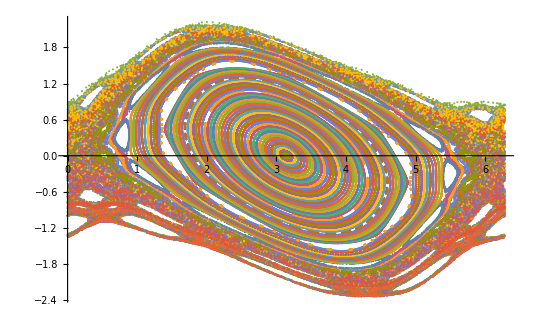

```mathematica
khere=0.9; (*Interesting structures at k=0.9*)
SectionSet = Table[sMapSection[Inits[[i,1]],Inits[[i,2]],khere,2000],{i,1,imax}];
ListPlot[SectionSet]
```

What we are looking at here are just some of the "strange" features to be found in strong Hamiltonian chaos :
   - Heteroclinic intersections : the stable/unstable manifolds of, say, a resonant chain and the original unstable equilibrium intersect . This implies a "heteroclinic tangle" connecting them and the possibility for chaotic particles to diffuse .
   
   (Warning, the standard map has a non-smooth δ(τ) = 1/(2π)Σ_n e^(2π i nτ) in the Hamiltonian. This is still multiplied by a smooth function in x, but the spectrum of resonances etc. tends to be richer than for a general system.)
   
   - The web of heteroclinic intersections can become so dense that only "regular islands" or "islands of stability survive" in a "sea of chaos" .
   
   - Many systems depending on a parameter ϵ have a “maximum” of the chaos and then the perturbation starts to dominate. However, the structure of the standard map implies that the “original” part of the Hamiltonian p^2/2 scales as ~K^2sin^2(x_typical)/2, so one keeps exploring more and more chaotic dynamics.

### Compute a Lyapunov exponent

-Graphics-
Let us compute a Lyapunov exponent of some of the chaotic regions above. We start by generating a small circle of initial conditions

```mathematica
khere=1.6;
xref=0.5; pref=0;
ϵ=10^-5;
```

```mathematica
CircPoints = 1000;
```

```mathematica
Circ = Table[{xref+ϵ Sin[i/CircPoints 2N[π]],pref+ϵ Cos[i/CircPoints 2N[π]]},{i,1,CircPoints}];
CircSet = Table[sMapSection[Circ[[i,1]],Circ[[i,2]],khere,100],{i,1,CircPoints}];
RefTraj = sMapSection[xref,pref,khere,100];
```

```mathematica
(*This takes the circle of initial conditions and evolves it by "iterations"*)
Manipulate[ListPlot[Table[{CircSet[[i,iteration,1]],CircSet[[i,iteration,2]]},{i,1,CircPoints}],PlotRange->{{0,2π},{-3,3}}],{iteration,1,100,1}]
```

To compute the exponent, one has to deal with competing limits, the ϵ->0 limit, and the t->∞ limit (or iterations-> ∞ for a discrete map). The issue is that sooner or later the dynamics become nonlinear. The circle can also expand into a finite space, so its exponential growth saturates. One must then take one  small ϵ and try to plot the size of the circle as a function of time:

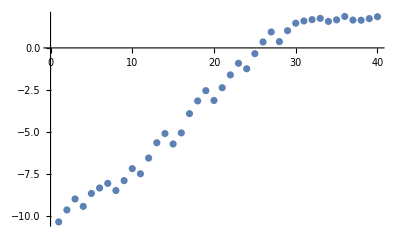

```mathematica
Sizes = Table[Max[Table[Sqrt[(CircSet[[i,iteration,1]]-RefTraj[[iteration,1]])^2+(CircSet[[i,iteration,2]]-RefTraj[[iteration,2]])^2],{i,1,CircPoints}]],{iteration,1,40}];
ListPlot[Log[Sizes]]
```

A crude estimate of the Lyapunov exponent is simply an estimate of the linear slope of the function

```mathematica
1/24 Log[Sizes[[25]]/Sizes[[1]]]
(*Or the inverse, gives you the characteristic number of iterations after you lose information about the system*)
24/Log[Sizes[[25]]/Sizes[[1]]]
```

0.418224

2.39106

### Why do some of the trajectories “stick” to the islands?

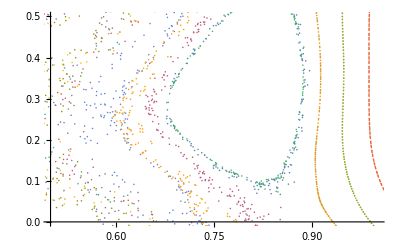

```mathematica
ListPlot[SectionSet,PlotRange->{{0.5,1},{0,0.5}}]
```

```mathematica
(*Let us take a closer look*)
khere = 0.9;
ListPlot[sMapSection[0.85,0,khere,1000000]]
ListPlot[sMapSection[0.85,0,khere,1000000],PlotRange->{{0.5,1},{0,0.5}}]
```

-Graphics-

-Graphics-

- We argued that the structure of perturbations of an integrable system implies recursion: the system produces resonant chains that have a phase space similar to nonlinear pendula. The nonlinear pendula themselves can have resonant chains in themselves. And so on. While these structures are exponentially suppressed as ϵ->0, at finite values of perturbation these may become significant. This can lead to fractal-like or outright fractal structures. 

 - The edges of regular islands can have a “fractal dust” of small islands near them. Diffusion in or around the fractal dust can be difficult. This leads to the phenomenon of “stickiness” seen above.
 
 - Another related structure are “cantori”, invariant sets that are reminiscent of KAM tori, but instead of being continuous, form a Cantor set - a fractal that is created by recursively taking parts out of a real line. They form semi-penetrable barriers for chaotic diffusion. 
 
 - A special role is played by tori that have a quasi-periodicity (ratio of frequencies) that is a “noble number”. Noble numbers are defined as numbers that are the “hardest to approximate” by rational numbers in the sense of continued fractions from some order of the continued fraction expansion. This makes them “hardest to break” by resonances. 
 
 - One would expect the “chaotic diffusion” process to follow some sort of diffusion equation with the Lyapunov coefficient as a characteristic time. As such, the time to escape a certain chaotic region as sampled throughout that region would  then be expected to be a distribution with a tail that goes as C exp(-λ t) with λ the largest Lyapunov exponent. 
 
 Unfortunately, this is not the case. The various fractal structures make it so that while escaping the region does occur at some (it is even guaranteed to occur), the distribution appears to have polynomial tails. Even strong chaos cannot be easily approximated as equivalent to “thermodynamics” or a stochastic system. It has transient semi-regular dynamics, seems to switch between “semi-local” values of Lyapunov exponents and so on. 
 
 Why is this important? One can show that in the sense of functional measure, integrable Hamiltonians of a a finite number of degrees of freedom larger than two have zero measure. At the same time, completely chaotic Hamiltonians are also of zero measure. That is, the dynamics shown above with all its weirdness, fractals, stickiness and all that, are in some sense the generic picture of low-degree-of-freedom dynamics. - Food for thought.